```mathematica
symbols={Subscript[s, 0],Subscript[s, 1],... Subscript[s, n]}
```

```mathematica
s ϵ p(Good,s)=Max[p(Good, s)]
```

```mathematica
p(C)
```

```mathematica
p(Subscript[F, i]|C)
```

```mathematica
p(Subscript[F, i])
```

```mathematica
p(C|Subscript[F, i])=p(C)∏_(i=0)^n (p(Subscript[F, i]|C))/(p(Subscript[F, i]))
```

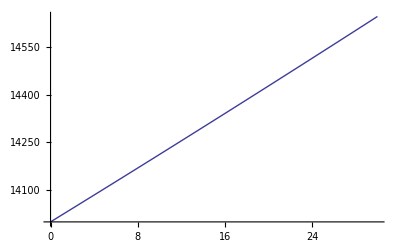

```mathematica
leverage=2.8;
win=0.7;
f[day_]:=14000*(1+leverage*0.02)^((3/5)day*win)*(1-leverage*0.04)^((3/5)day*(1-win))
Plot[f[day], {day,0,30}]
```